```mathematica
(*Documentatiopn : SoundNote[]/more information/applications*)
```

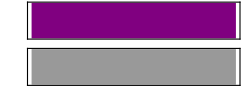

```mathematica
Sound[SoundNote[0]]
```

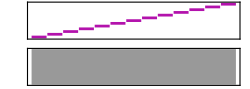

```mathematica
Sound[Table[SoundNote[i,0.1,"Violin"],{i,0,12}]]
```

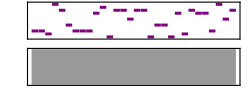

```mathematica
Sound[SoundNote/@RandomInteger[12,30],2]
```

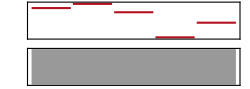

```mathematica
Sound[SoundNote[#,0.5, "Polysynth"]&/@{2,4,0,-12,-5}]
```

```mathematica
(*Generate a simple WolframTones-like composition:*)
```

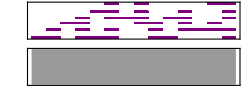

```mathematica
Sound[SoundNote[#,1/6,"Piano"]&/@(Pick[{0,5,9,12,16,21},#,1]&/@CellularAutomaton[30,{{1,0,0,0,0,0},0},13,{13,5}])]
```

```mathematica
CellularAutomaton[30,{{1,0,0,0,0,0},0},13,{13,5}]
```

{{1,0,0,0,0,0},{1,1,0,0,0,0},{0,0,1,0,0,0},{1,1,1,1,0,0},{1,0,0,0,1,0},{1,1,0,1,1,1},{0,0,0,1,0,0},{0,0,1,1,1,1},{1,1,1,0,0,0},{1,0,0,1,0,0},{0,1,1,1,1,0},{0,1,0,0,0,0},{0,1,1,0,0,1},{1,1,0,1,1,1}}

```mathematica
Pick[{a,b,c,d,e},{1,0,1,0,0},1]
```

{a,c}

```mathematica
Pick[{{a,b,c},{d,e,f}},{{1,0,0},{0,1,1}},1]
```

{{a},{e,f}}

```mathematica
(Pick[{0,5,9,12,16,21},#,1]&/@CellularAutomaton[30,{{1,0,0,0,0,0},0},13,{13,5}])
```

{{0},{0,5},{9},{0,5,9,12},{0,16},{0,5,12,16,21},{12},{9,12,16,21},{0,5,9},{0,12},{5,9,12,16},{5},{5,9,21},{0,5,12,16,21}}

```mathematica
14/6//N
```

2.33333

```mathematica
(*Play a cellular automaton sound:*)
```

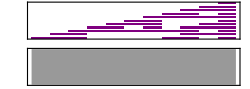

```mathematica
Sound[SoundNote[DeleteCases[3 Range[11] Reverse[#], 0] - 48, .1] & /@ Transpose[CellularAutomaton[110, {{1}, 0}, 10]]]
```

```mathematica
CellularAutomaton[110, {{1}, 0}, 10]
```

{{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,0,1,1,1,1,1},{0,0,0,0,0,1,1,0,0,0,1},{0,0,0,0,1,1,1,0,0,1,1},{0,0,0,1,1,0,1,0,1,1,1},{0,0,1,1,1,1,1,1,1,0,1},{0,1,1,0,0,0,0,0,1,1,1},{1,1,1,0,0,0,0,1,1,0,1}}

```mathematica
(*Play a random sequence of notes from different instruments:*)
```

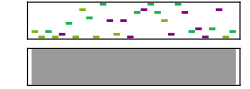

```mathematica
Sound[SoundNote[#,1,RandomChoice[{"Piano","Cello","Tuba"}]]& /@ RandomInteger[12, 30], 4]
```

```mathematica
Sin/@{1,2}
```

{Sin[1],Sin[2]}

```mathematica
Sin[#]&/@{1,2}
```

{Sin[1],Sin[2]}

```mathematica
f[#1,#2]&[a,b]
```

f[a,b]

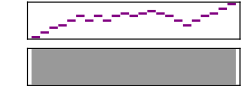

```mathematica
Sound[SoundNote/@({5,7,9,10,12,14,12,14,12,14,15,14,15,16,15,14,12,10,12,14,15,17,19}-6),4]
```